```mathematica
Quit[];
```

```mathematica
SetDirectory["~/Documents/Univ/phase_space_stoc/git/num/AndoVennin"]
```

/Users/yuichirotada/Documents/Univ/phase_space_stoc/git/num/AndoVennin

### double chaotic SR

```mathematica
model="double_chaotic";
```

```mathematica
fndata=Import[model<>"/Mn_"<>model<>"_SR.dat"];
trajdata=Import[model<>"/traj_"<>model<>"_SR.dat"];
calPdata=Import[model<>"/calP_"<>model<>"_SR.dat"];
```

```mathematica
f1List=Table[{fndata[[i,1]],fndata[[i,2]],fndata[[i,3]]},{i,1,Length[fndata],5}];
g2List=Table[{fndata[[i,1]],fndata[[i,2]],Log10[fndata[[i,4]]]},{i,1,Length[fndata],5}];
phivschi=Table[{trajdata[[i,2]],trajdata[[i,3]]},{i,Length[trajdata]}];
meancalP=Table[{calPdata[[i,1]],calPdata[[i,2]]±calPdata[[i,3]]},{i,Length[calPdata]}];
```

```mathematica
Show[ListContourPlot[f1List,FrameLabel->{"ϕ/M_Pl","ψ/M_Pl"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right]],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Export[model<>"/N.pdf",Show[ListContourPlot[f1List,FrameLabel->{"ϕ/M_Pl","ψ/M_Pl"},PlotLegends->BarLegend[Automatic,LegendLabel->⟨𝒩⟩]],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]];
```

```mathematica
Show[ListContourPlot[g2List,FrameLabel->{"ϕ/M_Pl","ψ/M_Pl"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right]],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Export[model<>"/dN2.pdf",Show[ListContourPlot[g2List,FrameLabel->{"ϕ/M_Pl","ψ/M_Pl"},PlotLegends->BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"]],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]];
```

```mathematica
dynfile=Import["../../../c++/output/doublechaotic_dyn.dat"];
calPcpp=Import["../../../c++/output/doublechaotic_spec.dat"];
```

```mathematica
aHList=Table[{dynfile[[i,1]],dynfile[[i,5]]},{i,Length[dynfile]}];
```

```mathematica
Nf=Last[aHList][[1]]
```

86.08

```mathematica
calPint=Interpolation[calPcpp];
```

```mathematica
calPcppvsN=Table[{Nf-1-aHList[[i,1]],calPint[aHList[[i,2]]]},{i,Length[aHList]}];
```

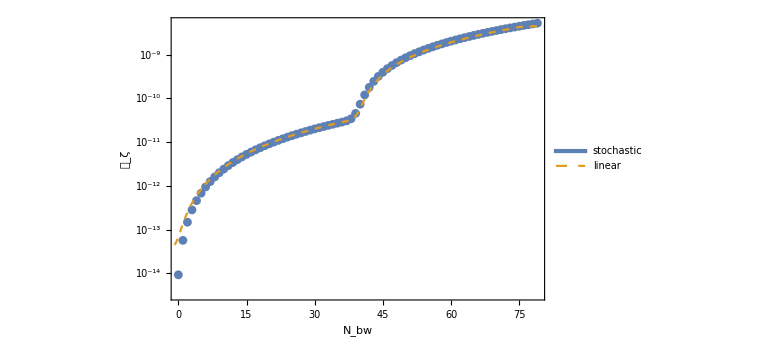

```mathematica
Show[ListLogPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},Joined->False,IntervalMarkers->"Fences"],ListLogPlot[{{{1,0},{2,0}},calPcppvsN},FrameLabel->{⟨𝒩⟩,Subscript[𝒫, ζ]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{"stochastic","linear"},LabelStyle->Directive[Larger,Black,FontFamily->"Optima"]],{0.8,0.2}]]]
```

### hybrid SR

```mathematica
model="hybrid";
```

```mathematica
Sample=Import[model<>"/sample_"<>model<>"_SR.dat"];
```

Import::nffil: File double_chaotic/sample_double_chaotic_SR.dat not found during Import.

```mathematica
phiSample=Table[{Sample[[i,1]],Sample[[i,2]]},{i,Length[Sample]}];
psiSample=Table[{Sample[[i,1]],Sample[[i,3]]},{i,Length[Sample]}];
VSample=Table[{Sample[[i,1]],Sample[[i,4]]},{i,Length[Sample]}];
```

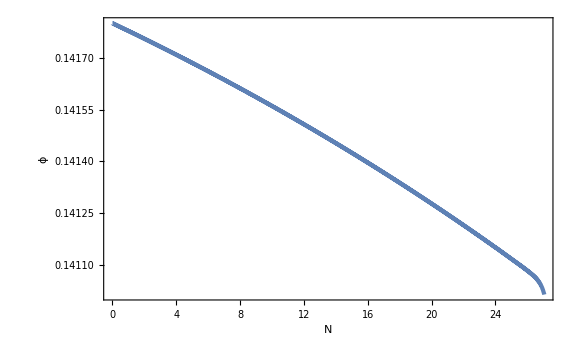

```mathematica
ListPlot[phiSample,FrameLabel->{N,ϕ}]
```

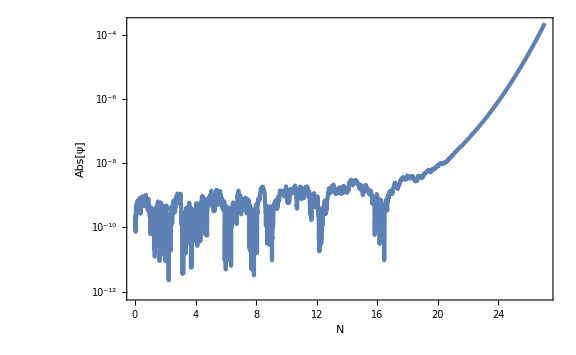

```mathematica
ListLogPlot[Abs[psiSample],FrameLabel->{N,Abs[ψ]}]
```

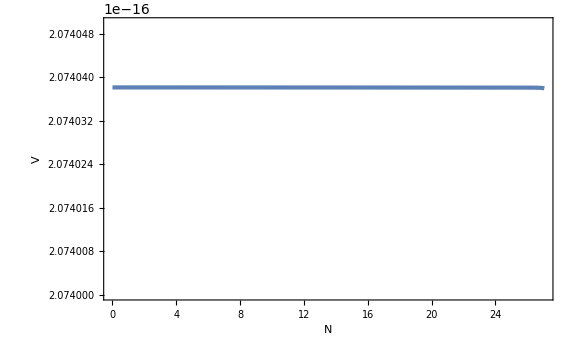

```mathematica
ListPlot[VSample,FrameLabel->{N,V},PlotRange->{2.074 10^-16,2.07405 10^-16}]
```

```mathematica
fndata=Sort[Select[Import[model<>"/Mn_"<>model<>"_SR.dat"],#[[2]]>0&]];
trajdata=Import[model<>"/traj_"<>model<>"_SR.dat"];
calPdata=Import[model<>"/calP_"<>model<>"_SR.dat"];
```

```mathematica
Last[trajdata]
```

{27.283,0.141008,0.000223324,0.000335977,2.15016×10^-15}

```mathematica
datared=1;
```

```mathematica
f1List=Table[{fndata[[i,1]],Log10[fndata[[i,2]]],fndata[[i,3]]},{i,1,Length[fndata],datared}];
g2List=Table[{fndata[[i,1]],Log10[fndata[[i,2]]],Log10[fndata[[i,4]]]},{i,1,Length[fndata],datared}];
phivschi=Table[{trajdata[[i,2]],Log10[Abs[trajdata[[i,3]]]]},{i,Length[trajdata]}];
Ndata=Table[{trajdata[[i,1]],trajdata[[i,4]]},{i,Length[trajdata]}];
dN2data=Table[{trajdata[[i,1]],trajdata[[i,5]]},{i,Length[trajdata]}];
meancalP=Table[{calPdata[[i,1]],calPdata[[i,2]]±calPdata[[i,3]]},{i,Length[calPdata]}];
```

```mathematica
Ncontour=Show[ListContourPlot[f1List,FrameLabel->{"ϕ/M_Pl","log_10(|ψ|/M_Pl)"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio,Contours->{{0,{Thick,Dotted}},2,5,10,15,20,25,30,35}],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Export[model<>"/N.pdf",Ncontour];
```

```mathematica
dN2contour=Show[ListContourPlot[g2List,FrameLabel->{"ϕ/M_Pl","log_10(|ψ|/M_Pl)"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio],ListPlot[phivschi,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Export[model<>"/dN2.pdf",dN2contour];
```

```mathematica
As=2.189 10^-9;
Π2=50;
M=0.1;
ϕc=0.1Sqrt[2];
μ2=11;
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

35355.3

2.07404×10^-16

```mathematica
ψ0=Sqrt[(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0)]
```

1.96975×10^-9

10.835

```mathematica
N1=(Sqrt[χ2]M ϕc^(1/2)μ1^(1/2))/2
N2=(M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2])
```

11.6378

0.537044

```mathematica
ξk[NN_]=-(N1+N2-NN)/(ϕc μ1);
χk[NN_]=(4ϕc μ1 ξk[NN]^2)/M^2;
ψk[NN_]=ψ0 Exp[χk[NN]];
```

```mathematica
calPCG[NN_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2 ψk[NN]^2);
```

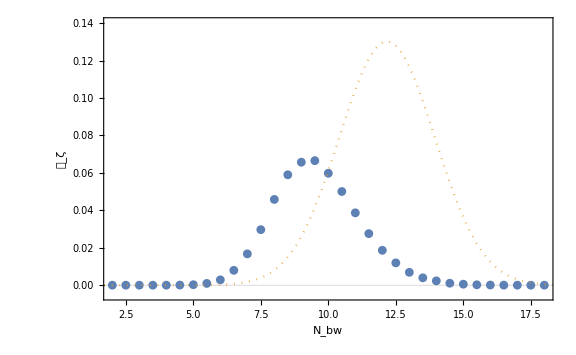

```mathematica
Show[ListPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->{{2,18},{-0.005,0.14}},GridLines->{None,{0}},Joined->False,IntervalMarkers->"Fences"],Plot[calPCG[NN],{NN,0,28},PlotStyle->{Color[2],Dotted}]]
```

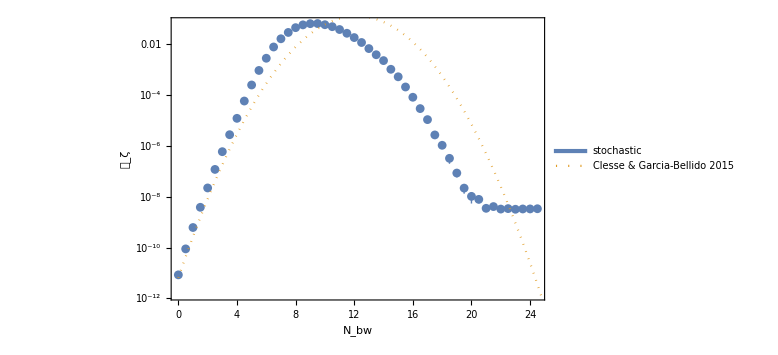

```mathematica
Show[ListLogPlot[meancalP,FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},Joined->False,IntervalMarkers->"Fences"],LogPlot[{0,calPCG[NN]},{NN,0,28},PlotStyle->{AbsoluteThickness[3],Dotted},PlotLegends->Placed[LineLegend[{"stochastic","Clesse & Garcia-Bellido 2015"},LabelStyle->Directive[Larger,Black,FontFamily->"Optima"]],{0.38,0.15}]]]
```

### Dhybrid SR

```mathematica
model="Dhybrid";
```

```mathematica
fndata1=Sort[Select[Import[model<>"/Mn_"<>model<>"_SR_D=1.dat"],#[[2]]>0&]];
trajdata1=Import[model<>"/traj_"<>model<>"_SR_D=1.dat"];
calPdata1=Import[model<>"/calP_"<>model<>"_SR_D=1.dat"];
fndata10=Sort[Select[Import[model<>"/Mn_"<>model<>"_SR_D=10.dat"],#[[2]]>0&]];
trajdata10=Import[model<>"/traj_"<>model<>"_SR_D=10.dat"];
calPdata10=Import[model<>"/calP_"<>model<>"_SR_D=10.dat"];
fndata100=Sort[Select[Import[model<>"/Mn_"<>model<>"_SR_D=100.dat"],#[[2]]>0&]];
trajdata100=Import[model<>"/traj_"<>model<>"_SR_D=100.dat"];
calPdata100=Import[model<>"/calP_"<>model<>"_SR_D=100.dat"];
fndata1000=Sort[Select[Import[model<>"/Mn_"<>model<>"_SR_D=1000.dat"],#[[2]]>0&]];
trajdata1000=Import[model<>"/traj_"<>model<>"_SR_D=1000.dat"];
calPdata1000=Import[model<>"/calP_"<>model<>"_SR_D=1000.dat"];
```

```mathematica
datared=1;
```

```mathematica
f1List1=Table[{fndata1[[i,1]],Log10[fndata1[[i,2]]],fndata1[[i,3]]},{i,1,Length[fndata1],datared}];
g2List1=Table[{fndata1[[i,1]],Log10[fndata1[[i,2]]],Log10[fndata1[[i,4]]]},{i,1,Length[fndata1],datared}];
phivschi1=Table[{trajdata1[[i,2]],Log10[Abs[trajdata1[[i,3]]]]},{i,Length[trajdata1]}];
Ndata1=Table[{trajdata1[[i,1]],trajdata1[[i,4]]},{i,Length[trajdata1]}];
dN2data1=Table[{trajdata1[[i,1]],trajdata1[[i,5]]},{i,Length[trajdata1]}];
meancalP1=Table[{calPdata1[[i,1]],calPdata1[[i,2]]±calPdata1[[i,3]]},{i,Length[calPdata1]}];
f1List10=Table[{fndata10[[i,1]],Log10[fndata10[[i,2]]],fndata10[[i,3]]},{i,1,Length[fndata10],datared}];
g2List10=Table[{fndata10[[i,1]],Log10[fndata10[[i,2]]],Log10[fndata10[[i,4]]]},{i,1,Length[fndata10],datared}];
phivschi10=Table[{trajdata10[[i,2]],Log10[Abs[trajdata10[[i,3]]]]},{i,Length[trajdata10]}];
Ndata10=Table[{trajdata10[[i,1]],trajdata10[[i,4]]},{i,Length[trajdata10]}];
dN2data10=Table[{trajdata10[[i,1]],trajdata10[[i,5]]},{i,Length[trajdata10]}];
meancalP10=Table[{calPdata10[[i,1]],calPdata10[[i,2]]±calPdata10[[i,3]]},{i,Length[calPdata10]}];
f1List100=Table[{fndata100[[i,1]],Log10[fndata100[[i,2]]],fndata100[[i,3]]},{i,1,Length[fndata100],datared}];
g2List100=Table[{fndata100[[i,1]],Log10[fndata100[[i,2]]],Log10[fndata100[[i,4]]]},{i,1,Length[fndata100],datared}];
phivschi100=Table[{trajdata100[[i,2]],Log10[Abs[trajdata100[[i,3]]]]},{i,Length[trajdata100]}];
Ndata100=Table[{trajdata100[[i,1]],trajdata100[[i,4]]},{i,Length[trajdata100]}];
dN2data100=Table[{trajdata100[[i,1]],trajdata100[[i,5]]},{i,Length[trajdata100]}];
meancalP100=Table[{calPdata100[[i,1]],calPdata100[[i,2]]±calPdata100[[i,3]]},{i,Length[calPdata100]}];
f1List1000=Table[{fndata1000[[i,1]],Log10[fndata1000[[i,2]]],fndata1000[[i,3]]},{i,1,Length[fndata1000],datared}];
g2List1000=Table[{fndata1000[[i,1]],Log10[fndata1000[[i,2]]],Log10[fndata1000[[i,4]]]},{i,1,Length[fndata1000],datared}];
phivschi1000=Table[{trajdata1000[[i,2]],Log10[Abs[trajdata1000[[i,3]]]]},{i,Length[trajdata1000]}];
Ndata1000=Table[{trajdata1000[[i,1]],trajdata1000[[i,4]]},{i,Length[trajdata1000]}];
dN2data1000=Table[{trajdata1000[[i,1]],trajdata1000[[i,5]]},{i,Length[trajdata1000]}];
meancalP1000=Table[{calPdata1000[[i,1]],calPdata1000[[i,2]]±calPdata1000[[i,3]]},{i,Length[calPdata1000]}];
```

```mathematica
Ncontour1=Show[ListContourPlot[f1List1,FrameLabel->{{"log_10(|ψ|/M_Pl)",None},{"ϕ/M_Pl",D==1}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio,Contours->{{0,{Thick,Dotted}},2,5,10,15,20,25,30,35}],ListPlot[phivschi1,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
dN2contour1=Show[ListContourPlot[g2List1,FrameLabel->{{"log_10(|ψ|/M_Pl)",None},{"ϕ/M_Pl",D==1}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio],ListPlot[phivschi1,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Ncontour10=Show[ListContourPlot[f1List10,FrameLabel->{{"log_10(|ψ|/M_Pl)",None},{"ϕ/M_Pl",D==10}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio,Contours->{{0,{Thick,Dotted}},2,5,10,15,20,25,30,35}],ListPlot[phivschi10,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
dN2contour10=Show[ListContourPlot[g2List10,FrameLabel->{{"log_10(|ψ|/M_Pl)",None},{"ϕ/M_Pl",D==10}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio],ListPlot[phivschi10,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Ncontour100=Show[ListContourPlot[f1List100,FrameLabel->{{"log_10(|ψ|/M_Pl)",None},{"ϕ/M_Pl",D==100}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio,Contours->{{0,{Thick,Dotted}},2,5,10,15,20,25,30,35}],ListPlot[phivschi100,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
dN2contour100=Show[ListContourPlot[g2List100,FrameLabel->{{"log_10(|ψ|/M_Pl)",None},{"ϕ/M_Pl",D==100}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio],ListPlot[phivschi100,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
Ncontour1000=Show[ListContourPlot[f1List1000,FrameLabel->{{"log_10(|ψ|/M_Pl)",None},{"ϕ/M_Pl",D==1000}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->⟨𝒩⟩],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio,Contours->{{0,{Thick,Dotted}},2,5,10,15,20,25,30,35}],ListPlot[phivschi1000,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
dN2contour1000=Show[ListContourPlot[g2List1000,FrameLabel->{{"log_10(|ψ|/M_Pl)",None},{"ϕ/M_Pl",D==1000}},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10⟨δ𝒩^2⟩"],Right],PlotRange->{{0.1409,0.142},{-10,-3}},AspectRatio->1/GoldenRatio],ListPlot[phivschi1000,PlotStyle->{{Color[4],AbsoluteThickness[5]}}]]
```

-Graphics-

```mathematica
ListPlot[{phivschi1,phivschi10,phivschi100,phivschi1000},FrameLabel->{"ϕ/M_Pl","log_10(|ψ|/M_Pl)"},PlotLegends->Placed[{D==1,10,100},{0.8,0.75}]]
```

-Graphics-

```mathematica
As=2.189 10^-9;
Π2=50;
M=0.1;
ϕc=0.1Sqrt[2];
μ2=11;
μ1=Π2/(M^2 ϕc)
Λ4=12 π^2 As/μ1^2
```

35355.3

2.07404×10^-16

```mathematica
ψ0=Sqrt[(Sqrt[2]Λ4 M ϕc^(1/2)μ1^(1/2))/(96 π^(3/2))]
χ2=Log[(ϕc^(1/2)M)/(2 μ1^(1/2)ψ0)]
```

1.96975×10^-9

10.835

```mathematica
N1=(Sqrt[χ2]M ϕc^(1/2)μ1^(1/2))/2
N2=(M ϕc^(1/2)μ1^(1/2))/(4Sqrt[χ2])
```

11.6378

0.537044

```mathematica
ξk[NN_]=-(N1+N2-NN)/(ϕc μ1);
χk[NN_]=(4ϕc μ1 ξk[NN]^2)/M^2;
ψk[NN_]=ψ0 Exp[χk[NN]];
```

```mathematica
calPCG[NN_]=(Λ4 M^2 ϕc μ1)/(192 π^2 χ2 ψk[NN]^2);
```

```mathematica
Show[ListPlot[{meancalP1,meancalP10,meancalP100,meancalP1000},FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},PlotRange->{{2,18},{-0.005,0.14}},GridLines->{None,{0}},Joined->False,IntervalMarkers->"Fences"],Plot[calPCG[NN],{NN,0,28},PlotStyle->{Dotted}]]
```

-Graphics-

```mathematica
Show[ListLogPlot[{meancalP1,meancalP10,meancalP100,meancalP1000},FrameLabel->{Subscript[N, bw],Subscript[𝒫, ζ]},Joined->False,IntervalMarkers->"Fences",PlotRange->{10^-12,1},PlotLegends->Placed[PointLegend[{D==1,10,100,1000},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.38,0.2}]],LogPlot[calPCG[NN],{NN,0,28},PlotStyle->Dotted,PlotLegends->Placed[LineLegend[{"CG15"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.38,0.2}]]]
```

-Graphics-